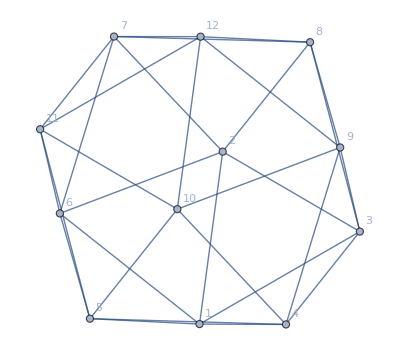

```mathematica
g1=Graph[plantri[[1]],VertexLabels->"Name"]
```

```mathematica
f1=FindFullFormula[g1];Length[f1]
```

26793

```mathematica
Map[StringCount[SymbolName[#],"x"]&,f1]//Tally//Sort
```

{{3,10},{4,660},{5,4908},{6,10008},{7,7900},{8,2800},{9,470},{10,36},{11,1}}

```mathematica
Select[f1,StringCount[SymbolName[#],"x"]==3&]
```

{v19bx25cx37ax468,v19bx24cx357x68a,v18ax29bx357x46c,v18bx259x37ax46c,v18bx24cx36ax579,v18ax24bx36cx579,v17ax29bx35cx468,v17ax259x36cx48b,v179x25cx36ax48b,v179x24bx35cx68a}

```mathematica
EdgeList[g1]//Length
```

30

```mathematica
GraphFromSets[SymbolToSets[v19bx25cx37ax468]]//Length
```

54

```mathematica
SetDifference[GraphFromSets[SymbolToSets[v19bx25cx37ax468]],EdgeList[g1]]
```

{1<->12,1<->7,1<->10,1<->8,2<->9,2<->11,2<->10,2<->4,5<->9,5<->7,5<->8,3<->11,3<->5,3<->12,3<->6,7<->9,4<->11,4<->12,4<->7,6<->9,6<->12,6<->10,8<->11,8<->10}

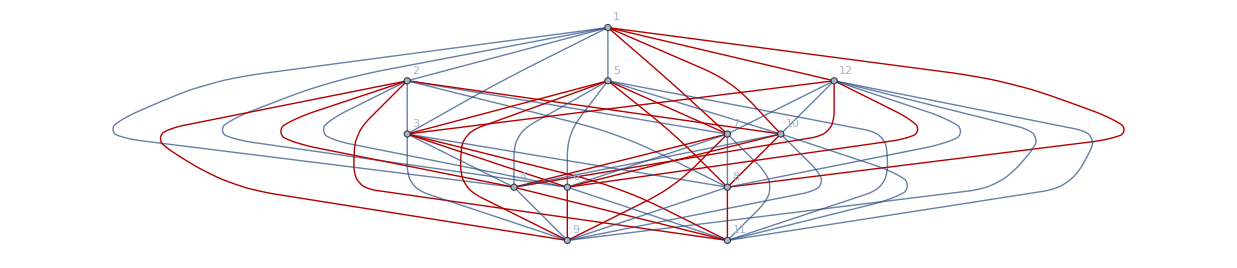

```mathematica
Graph[GraphFromSets[SymbolToSets[v19bx25cx37ax468]], GraphHighlight-> SetDifference[GraphFromSets[SymbolToSets[v19bx25cx37ax468]],EdgeList[g1]],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
IntegerPartitions[15,{4}]
```

{{12,1,1,1},{11,2,1,1},{10,3,1,1},{10,2,2,1},{9,4,1,1},{9,3,2,1},{9,2,2,2},{8,5,1,1},{8,4,2,1},{8,3,3,1},{8,3,2,2},{7,6,1,1},{7,5,2,1},{7,4,3,1},{7,4,2,2},{7,3,3,2},{6,6,2,1},{6,5,3,1},{6,5,2,2},{6,4,4,1},{6,4,3,2},{6,3,3,3},{5,5,4,1},{5,5,3,2},{5,4,4,2},{5,4,3,3},{4,4,4,3}}

```mathematica
GeneratePartitionTypes[k_,n_:4]:=Block[{result={},current,sets},
Table[
current=1;
sets={};
Table[
sets=Append[sets,Range[current, current+count-1]];
current+=count;
,{count,part}
];
result=Append[result,sets].
,{part,IntegerPartitions[k,{n}]}
];
result
]
```

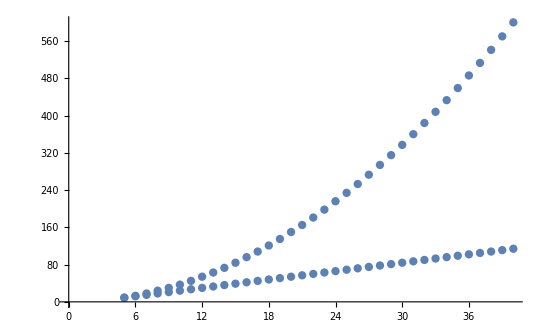

```mathematica
Flatten[Table[
With[{list=Table[EdgeCount[GraphFromSets[part]],{part,GeneratePartitionTypes[k,4]}]},
{{k,Min[list]},{k,Max[list]}}],
{k,5,40}
],1]//ListPlot
```

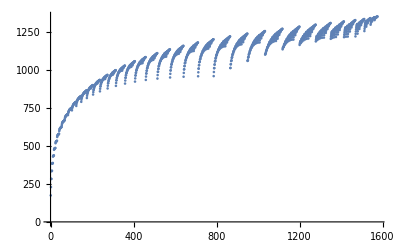

```mathematica
ListPlot[Table[EdgeCount[GraphFromSets[part]],{part,GeneratePartitionTypes[60,4]}]]
```

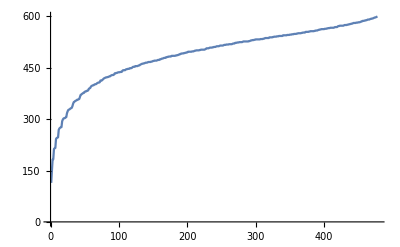

```mathematica
ListLinePlot[Sort[Table[EdgeCount[GraphFromSets[part]],{part,GeneratePartitionTypes[40,4]}]]]
```

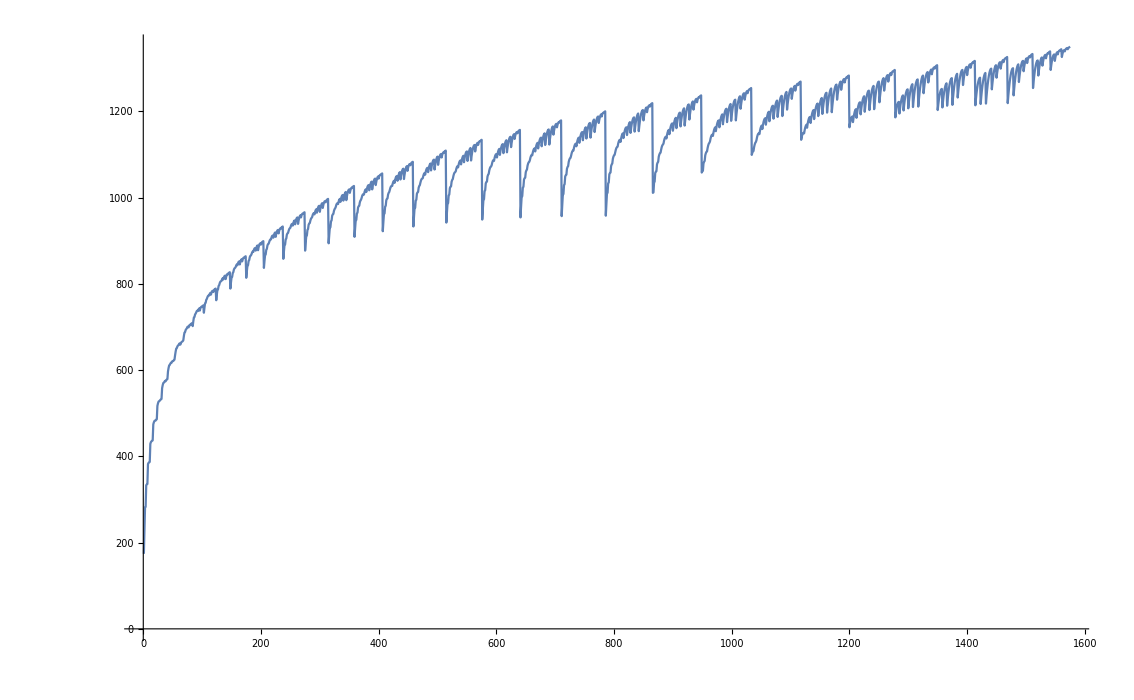

```mathematica
ListLinePlot[Table[EdgeCount[GraphFromSets[part]],{part,GeneratePartitionTypes[60,4]}]]
```

```mathematica
StirlingS2[60,57]
```

806060655

```mathematica
Length[IntegerPartitions[20,{4}]]
```

64

```mathematica
PartitionsP[15]
```

176

```mathematica
PartitionsQ[20]
```

64

```mathematica
Table[Length[IntegerPartitions[k,{4}]]-PartitionsQ[k],{k,1,100}]
```

{-1,-1,-2,-1,-2,-2,-2,-1,-2,-1,-1,0,0,1,0,2,1,1,0,0,-4,-5,-10,-14,-22,-29,-42,-53,-71,-90,-115,-141,-178,-215,-264,-317,-382,-453,-541,-635,-749,-875,-1022,-1184,-1376,-1584,-1826,-2094,-2400,-2738,-3125,-3549,-4031,-4564,-5163,-5823,-6567,-7383,-8297,-9305,-10426,-11659,-13033,-14538,-16209,-18045,-20072,-22296,-24754,-27443,-30406,-33652,-37218,-41118,-45404,-50081,-55210,-60812,-66939,-73623,-80934,-88895,-97589,-107059,-117382,-128613,-140853,-154152,-168627,-184355,-201448,-220001,-240160,-262016,-285738,-311452,-339328,-369520,-402238,-437640}